```mathematica
Clear["Global`*"];

(* Exploitation parameter *)
beta = {beta1,beta2}; 
(* Learning rate *)
alpha = {alpha1,alpha2};
(* Discount factor *)
gamma = {gamma1,gamma2};

(* Reward matrix *)
(* r_i,a1,a2 *)
RM = {{{r111,r112},{r121,r122}},{{r211,r212},{r221,r222}}};

(* Q-table *)
(* q_i,a *)
Q = {{q11,q12},{q21,q22}};

(* Behavior profiles as functions of Q *)
(* x_i,a *)
Z=Total[Exp[beta*Q],{2}];
XQ = Exp[beta*Q]/Z;

(* Behavior profiles as independent variables *)
(* x_i,a *)
X = {{X11,X12},{X21,X22}};

(* Q as functions of X *)
QX = Log[X]/beta ;
(*QX = QX + Log[Z]*)
QXrule=Thread[Flatten[Q] -> Flatten[QX]];

(* Joint behavioral profile *)
(* Xvec_a1,a2 *)
Xs = Times @@{{{X11,X11},{X12,X12}},{{X21,X22},{X21,X22}}};
```

```mathematica
(* Epsilon greedy stuff *)
Q1H[Qi_] := If[Qi[[1]] > Qi[[2]], 1, 0]
eps1[Qi_] := If[Qi[[1]]<Qi[[2]], epsilon,1-epsilon]
QXeps = {{Q1H[Q[[1]]]*(1-epsilon) + (1-Q1H[Q[[1]]])*epsilon,Q1H[Q[[1]]]*epsilon + (1-Q1H[Q[[1]]])*(1-epsilon)},{Q1H[Q[[2]]]*(1-epsilon) + (1-Q1H[Q[[2]]])*epsilon,Q1H[Q[[2]]]*epsilon + (1-Q1H[Q[[2]]])*(1-epsilon)}};
```

```mathematica
QXruleeps = Thread[Flatten[Q] -> Flatten[QXeps]];
```

```mathematica
(* Deterministic limit (Eq. 17) ------------------------------------------------------------*)

Clear[alpha1,alpha2,beta1,beta2,gamma1,gamma2];
(* a'<R>_i,a (Given a_i, average over other agent's action a_i' to get average R_i) *)
Risa =ConstantArray[0,{2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*a*)
For[j1=1,j1<3,j1++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i2;a2=j1;,iother=1;a1=j1;a2=i2;];
(* Boltzmann exploration *)
Prob=XQ[[iother,j1]];
(* Epsilon greedy *)
(*If[j1==1,Prob=eps1[Q[[iother]]],Prob=1-eps1[Q[[iother]]]];*)

Risa[[i1,i2]] += Prob*RM[[i1,a1,a2]];
]]];

(* a'<maxQ>_i,a (Given a_i, average over other agent's action a_i' to get average maxQ_i) *)
maxQisa = ConstantArray[0,{2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*a*)
For[j1=1,j1<3,j1++,(*a'*)
(* Other agent's id *)
If[i1==1,iother=2;a1=i2;a2=j1;,iother=1;a1=j1;a2=i2;];
(* Boltzmann exploration *)
Prob=XQ[[iother,j1]];
(* Epsilon greedy *)
(*If[j1==1,Prob=eps1[Q[[iother]]],Prob=1-eps1[Q[[iother]]]];*)

maxQisa[[i1,i2]] +=Prob*Max[Q[[i1]]];
]]];

(* TD_i,a (Eq. 17 in terms of q) *)
TD=(1-gamma) * Risa + gamma*maxQisa-Q;

(* Variable change q -> X *)
RuleProb = {X12 -> 1-X11,X22->1-X21}; (* Normalization *)

(* Boltzmann *)
TD11X = TD[[1,1]] /. QXrule/.RuleProb;
TD12X = TD[[1,2]] /. QXrule/.RuleProb;
TD21X = TD[[2,1]] /. QXrule/.RuleProb;
TD22X = TD[[2,2]] /. QXrule/.RuleProb;

(* Epsilon greedy *)
TD11X = TD[[1,1]] /. QXruleeps/.RuleProb;
TD12X = TD[[1,2]] /. QXruleeps/.RuleProb;
TD21X = TD[[2,1]] /. QXruleeps/.RuleProb;
TD22X = TD[[2,2]] /. QXruleeps/.RuleProb;
```

```mathematica
(* X evolution equation (Eq. 11) ------------------------------------------------------------*)
X11next=X11*Exp[alpha1*beta1*TD11X]/(X11*Exp[alpha1*beta1*TD11X]+(1-X11)*Exp[alpha1*beta1*TD12X]);
X21next=X21*Exp[alpha2*beta2*TD21X]/(X21*Exp[alpha2*beta2*TD21X]+(1-X21)*Exp[alpha2*beta2*TD22X]);
```

```mathematica
(* Two-state penny matching game ------------------------------------------------------------------------------------*)

(* r_i,a1,a2 *)
r111=1;r112=0;r121=0;r122=1; (* Agent 1 is keeper *)
r211=0;r212=1;r221=1;r222=0;
```

```mathematica
(* Two-state IPD ------------------------------------------------------------------------------------*)

(* r_i,s,a1,a2 *)
r111=3;r112=0;r121=10;r122=2; 
r211=3;r212=10;r221=0;r222=2;
```

```mathematica
(* Chicken Game *)

(* r_i,s,a1,a2 *)
r111=-2;r112=1;r121=-1;r122=0;
r211=-2;r212=-1;r221=1;r222=0;
```

```mathematica
X11nextP = X11next /. Params;
X21nextP = X21next /. Params;
```

```mathematica
Solve[{X11nextP-X11==0,X21nextP-X21==0},{X11,X21}]
```

Xnext

```mathematica
(* Set hyperparameters ---------------------------------------------------------------------*)
Params = {alpha1->0.1,alpha2->0.1,beta1->0.5,beta2->5,gamma1->0,gamma2->0};
X11next-X11 /. {X11->0.5,X21->0.5} /. Params;

Xnext = {X11next-X11, X21next-X21};
Jacob = D[Xnext,{{X11,X21}}];
FullSimplify[Eigenvalues[Jacob /. {X11->0.5,X21->0.5,alpha2->alpha1,gamma1->0,gamma2->0}]]
```

{Piecewise[{{-1. Tanh[alpha1 beta2 (-1+2 epsilon)]^2, (2 epsilon<1&&q11≤q12)⊻(q11≤q12&&2 epsilon≤1)⊻2 epsilon≤1⊻q11≤q12⊻q21≤q22}, {0, True}}],Piecewise[{{-1. Tanh[alpha1 beta1 (-1+2 epsilon)]^2, (2 epsilon<1&&q21≤q22)⊻(q21≤q22&&2 epsilon≤1)⊻2 epsilon≤1⊻q11≤q12⊻q21≤q22}, {0, True}}]}

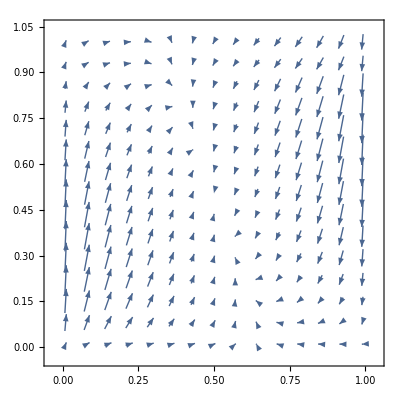

Export::noopen: Cannot open D:\USB_send\Project_Negotiation\prospectiveporpoise\beta1=0.5beta2=5.pdf.

```mathematica
(* Plot -----------------------------------------------------------------------------------*)
(* Observations: the agent with greater alpha seems to be setting the dynamics (changing the other agent's parameters don't change anything) *)
(* Setting smaller gamma seems to be better *)
myPlot=VectorPlot[{X11next-X11/.Params,X21next-X21/.Params},{X11,0.01,0.99},{X21,0.01,1}]
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\beta1=0.5beta2=5.pdf",Style[myPlot,Magnification->1],ImageResolution->2000];
```

```mathematica
(* Appendix A Alternative -------------------------------------------------------------------*)
 TDRules = TD /. QXrule/.RuleProb; (* i,s,a *)
Aisa=X * Exp[alpha * beta * TDRules];
Simplify[Aisa[[1,1,1]]]
```

ⅇ^(alpha1 beta1 ((1-gamma1) (-r1112 (t1121+t1122) (-1+X211)+r1111 (t1111+t1112) X211)-Log[X111]/beta1+gamma1 ((t1121+t1111 X211-t1121 X211) Max[Log[1-X111]/beta1,Log[X111]/beta1]+(t1122+t1112 X211-t1122 X211) Max[Log[1-X121]/beta1,Log[X121]/beta1]))) X111

```mathematica
(* Numerical Simulation ---------------------------------------------------------------------*)TimeSteps = 1000; (* Number of time steps *)

(* Initial conditions *)
Qvals = {{{0,0.916},{0.829,1}},{{0.916,0},{0.921,1}}};

(* Agent parameters *)
alpha1 = 0.8;
alpha2 = 0.8;
beta1 = 8.0;
beta2 = 8.0;
gamma1 = 0.1;
gamma2 = 0.1;

(* Record probabilities *)
X111List={};(* Agent 1, state 1 *)
X211List={};(* Agent 2, state 1 *)
X121List={};(* Agent 1, state 2 *)
X221List={};(* Agent 2, state 2 *)

For[t=0, t<TimeSteps, t++,
	
	Qvals = Qvals + alpha*TD /.Thread[Flatten[Q]->Flatten[Qvals]];
	X111List = Append[X111List,XQ[[1,1,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X211List = Append[X211List,XQ[[2,1,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X121List = Append[X121List,XQ[[1,2,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
	X221List = Append[X221List,XQ[[2,2,1]] /.Thread[Flatten[Q]->Flatten[Qvals]] ];
]
```

```mathematica
(* Appendix A -----------------------------------------------------------------------------*)

(* Series expression from probability condition *)
Xseries = 1 +2*X-Total[X,{3}];
Xserieswhole = Times @@ Xseries;

(* A6 (derivative) ------------------------------------------*)
(* dX_i,s,a / dX_j,r,b *)
A6 = D[Xseries,{X,1}];

(* A15 ---------------------------------------------------- *)
(* dX_vec_s,a1,a2 / dX_j,r,b *) (* Action pair differentiation *)
dXdX = ConstantArray[0,{2,2,2,2,2,2}];
For[i1=1,i1<3,i1++, (*s*)
For[i2=1,i2<3,i2++,(*a1*)
For[i3=1,i3<3,i3++,(*a2*)
For[i4=1,i4<3,i4++,(*j*) (* Agent being differentiated *)
For[i5=1,i5<3,i5++,(*r*)
For[i6=1,i6<3,i6++,(*b*)
If[i4==1,iother=2;aother=i3;adiff=i2;,iother=1;aother=i2;adiff=i3;]; (* Get the differentiated agent's action and other guy's index and action *)
dXdX[[i1,i2,i3,i4,i5,i6]] += X[[iother,i1,aother]]*A6[[i4,i1,adiff,i4,i5,i6]];
]]]]]];

(* d_s',a1,a2<R>_i,s / dX_j,r,b *)
A15 = ConstantArray[0,{2,2,2,2,2}]; (* Initialize *)
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*j*)
For[i4=1,i4<3,i4++,(*r*)
For[i5=1,i5<3,i5++,(*b*)
For[j1=1,j1<3,j1++,(*s'*)
For[j2=1,j2<3,j2++,(*a1*)
For[j3=1,j3<3,j3++,(*a2*)
A15[[i1,i2,i3,i4,i5]] +=dXdX[[i2,j2,j3,i3,i4,i5]]*T[[i2,j2,j3,j1]]*RM[[i1,i2,j2,j3]];
]]]]]]]];

(* A14 ---------------------------------------------------- *)
(* d_a1,a2<T>_s,s' / dX_j,r,b *) (* A12 where a is not fixed *)
A12unfix = ConstantArray[0,{2,2,2,2,2,2}];
(* i's = indices, j's = summation *)
For[i1=1,i1<3,i1++, (*s*)
For[i2=1,i2<3,i2++,(*s'*)
For[i3=1,i3<3,i3++,(*j*)
For[i4=1,i4<3,i4++,(*r*)
For[i5=1,i5<3,i5++,(*b*)
For[j1=1,j1<3,j1++,(*a1*)
For[j2=1,j2<3,j2++,(*a2*)
A12unfix[[i1,i2,i3,i4,i5]] +=dXdX[[i1,j1,j2,i3,i4,i5]]*T[[i1,j1,j2,i2]];
]]]]]]];

(* dM_i,s,s' / dX_j,r,b *)
A14 = ConstantArray[0,{2,2,2,2,2,2}];
For[i1=1,i1<3,i1++, (*i*)
For[i2=1,i2<3,i2++,(*s*)
For[i3=1,i3<3,i3++,(*s'*)
For[i4=1,i4<3,i4++,(*j*)
For[i5=1,i5<3,i5++,(*r*)
For[i6=1,i6<3,i6++,(*b*)
A14[[i1,i2,i3,i4,i5,i6]] = -gamma[[i1]] * A12unfix[[i2,i3,i4,i5,i6]];
]]]]]];



(* A14 ---------------------------------------------------- *)
```